# Woods-Saxon Well Potential

Authors: Angel Salazar, Quray Potosi
School Of Physical Sciences and Nanotechnology

```mathematica
V0=-1;
L=2;
```

```mathematica
Vx[x_,a_]:= V0 (HeavisideTheta[-x]/(1+Exp[-a(x+L)])+HeavisideTheta[x]/(1+Exp[a (x-L)]));
```

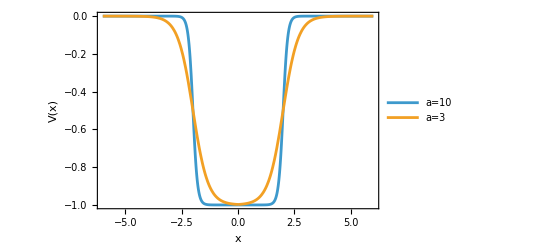

```mathematica
Plot[{Vx[x,10],Vx[x,3]},{x,-6,6},PlotRange->All,Frame->True,FrameLabel->{"x","V(x)"},PlotLegends->{"a=10","a=3"}]
```

## Bound States

### For x<0 :

```mathematica
Clear[V0,a,L];
```

```mathematica
eq1= Subscript[ϕ, L]''[x] + ((En+V0/(1+Exp[-a(x+L)]))^2-1) Subscript[ϕ, L][x]==0;
```

Let

```mathematica
y[x_]:=(1+Exp[-a(x+L)])^-1
```

```mathematica
eq1/.{Subscript[ϕ, L]''[x]-> a^2 y(1-y) D[y(1-y)  D[Subscript[ϕ, L][y],y],y]}
```

(-1+(En+V0/(1+ⅇ^(-a (L+x))))^2) ϕ_L[x]+a^2 (1-y) y ((1-y) ϕ_L'[y]-y ϕ_L'[y]+(1-y) y ϕ_L''[y])==0

```mathematica
eq2 = (-1+(En+V0/y)^2) Subscript[ϕ, L][x]+a^2 (1-y) y ((1-y) Subscript[ϕ, L]'[y]-y Subscript[ϕ, L]'[y]+(1-y) y Subscript[ϕ, L]''[y])==0
```

(-1+(En+V0/y)^2) ϕ_L[x]+a^2 (1-y) y ((1-y) ϕ_L'[y]-y ϕ_L'[y]+(1-y) y ϕ_L''[y])==0

Let

```mathematica
Subscript[ϕ, L][y_]:= y^σ(1-y)^-γ h[y];
```

```mathematica
eq3=a^2 y(1-y) D[y(1-y)  D[Subscript[ϕ, L][y],y]]//FullSimplify
```

a^2 (1-y)^-γ (-1+y) y^(1+σ) (-((y (γ-σ)+σ) h[y])+(-1+y) y h'[y])

Substituting equation 3 into equation 2 we get:

```mathematica
eq4= (-1+(En-V0/y)^2) Subscript[ϕ, L][y]+a^2 (1-y)^-γ (-1+y) y^(1+σ) (-((y (γ-σ)+σ) h[y])+(-1+y) y h'[y])==0
```

(-1+(En-V0/y)^2) (1-y)^-γ y^σ h[y]+a^2 (1-y)^-γ (-1+y) y^(1+σ) (-((y (γ-σ)+σ) h[y])+(-1+y) y h'[y])==0

Expand the first term in equation 4

```mathematica
-1+((En y-V0)^2//ExpandAll)/y^2
```

-1+(V0^2-2 En V0 y+En^2 y^2)/y^2

Replace in equation 4 :

```mathematica
eq4= (-1+(V0^2-2 En V0 y+En^2 y^2)/y^2) (1-y)^-γ y^σ h[y]+a^2 (1-y)^-γ (-1+y) y^(1+σ) (-((y (γ-σ)+σ) h[y])+(-1+y) y h'[y])==0 //Simplify
```

(1-y)^-γ y^(-1+σ) ((V0^2-2 En V0 y+y^2 (-1+En^2-a^2 (-1+y) y (y γ+σ-y σ))) h[y]+a^2 (-1+y)^2 y^4 h'[y])==0

Then  solving the hypergeometric differential equation we get:

```mathematica
eq5 = y (1-y) h''[y] + ((1+2 σ)-2( σ +γ+1) y )h'[y]-(1/2+σ+γ+λ)(1/2+σ+γ-λ) h[y]==0
```

-((1/2+γ-λ+σ) (1/2+γ+λ+σ) h[y])+(1+2 σ-2 y (1+γ+σ)) h'[y]+(1-y) y h''[y]==0

Where

```mathematica
σ[En_,a_]:=(√(1-En^2))/a;
γ[En_,V0_,a_]:=(√(1-(En+V0)^2))/a;
λ[En_,V0_,a_]:=(√(a^2-4 V0^2))/(2 a);
```

The solution of equation 5 can be expressed in terms of Gauss hypergeometric functions as:

```mathematica
h[y]= a1 Hypergeometric2F1[1/2+γ+σ-λ,1/2+γ+σ+λ,1+2 σ,y]+a2 y^(-2σ)Hypergeometric2F1[1/2+γ-σ-λ,1/2+γ-σ+λ,1-2σ,y];
```

The we get

```mathematica
Subscript[ϕ, L][y]
```

(1-y)^-γ y^σ (a2 y^(-2 σ) Hypergeometric2F1[1/2+γ-λ-σ,1/2+γ+λ-σ,1-2 σ,y]+a1 Hypergeometric2F1[1/2+γ-λ+σ,1/2+γ+λ+σ,1+2 σ,y])

Thus we define

```mathematica
ϕL[x_,En_]:=a1 y[x]^σ[En] (1-y[x])^γ[En] Hypergeometric2F1[1/2+γ[En]+σ[En]-λ[En],1/2+γ[En]+σ[En]+λ[En],1+2 σ[En],y[x]]+ a2 y[x]^(-σ[En])(1-y[x])^γ[En] Hypergeometric2F1[1/2+γ[En]-σ[En]-λ[En],1/2+γ[En]-σ[En]+λ[En],1-2 σ[En],y[x]]
```

### For x>0 :

```mathematica
Clear[V0,a,L];
```

```mathematica
eqR1= Subscript[ϕ, R]''[x] + ((En+V0/(1+Exp[a(x-L)]))^2-1) Subscript[ϕ, R][x]==0;
```

Let

```mathematica
z[x_]:=1/(1+Exp[a(x-L)])
```

```mathematica
z'[x]
```

-(a ⅇ^(a (-L+x)))/((1+ⅇ^(a (-L+x)))^2)

Thus, dϕR[x]/dz is:

```mathematica
Subscript[ϕ, R]'[z] z'[x]
```

-(a ⅇ^(a (-L+x)) ϕ_R'[z])/((1+ⅇ^(a (-L+x)))^2)

and (d^2 ϕR[x])/dz^2 is:

```mathematica
-(a ⅇ^(a (L+x)) Subscript[ϕ, R]'[z])/((1+ⅇ^(a (L+x)))^2) D[-(a ⅇ^(a (L+x)) Subscript[ϕ, R]'[z])/((1+ⅇ^(a (L+x)))^2),z]
```

(a^2 ⅇ^(2 a (L+x)) ϕ_R'[z] ϕ_R''[z])/((1+ⅇ^(a (L+x)))^4)

Therefore

```mathematica
eqR1/.{1/(1+Exp[a(x-L)])->z, Subscript[ϕ, R]''[x] -> (a^2 ⅇ^(2 a (L+x)) Subscript[ϕ, R]'[z] Subscript[ϕ, R]''[z])/((1+ⅇ^(a (L+x)))^4)}
```

(-1+(En+V0 z)^2) ϕ_R[x]+(a^2 ⅇ^(2 a (L+x)) ϕ_R'[z] ϕ_R''[z])/((1+ⅇ^(a (L+x)))^4)==0

Let

```mathematica
Subscript[ϕ, R][z_]:= z^σ(1-z)^-γ g[z];
```

```mathematica
eqR3=a^2 z(1-z) D[z (1-z)  D[Subscript[ϕ, R][z],z],z ]//FullSimplify
```

a^2 (1-z)^-γ z^σ ((z^2 (-1+γ-σ) (γ-σ)+σ^2+z (γ-σ) (1+2 σ)) g[z]+(-1+z) z ((-1-2 σ+2 z (1-γ+σ)) g'[z]+(-1+z) z g''[z]))

Substituting equation 3 into equation 2 we get:

```mathematica
eqR4= (-1+(En-V0 z)^2) Subscript[ϕ, R][z]+a^2 (1-z)^-γ z^σ ((z^2 (-1+γ-σ) (γ-σ)+σ^2+z (γ-σ) (1+2 σ)) g[z]+(-1+z) z ((-1-2 σ+2 z (1-γ+σ)) g'[z]+(-1+z) z g''[z]))==0 //Simplify
```

(1-z)^-γ z^σ ((-1+(En-V0 z)^2) g[z]+a^2 ((z^2 (-1+γ-σ) (γ-σ)+σ^2+z (γ-σ) (1+2 σ)) g[z]+(-1+z) z ((-1-2 σ+2 z (1-γ+σ)) g'[z]+(-1+z) z g''[z])))==0

Expand the first term in equation 4

```mathematica
(-1+(En-V0 z)^2) Subscript[ϕ, R][z]//Expand
```

-(1-z)^-γ z^σ g[z]+En^2 (1-z)^-γ z^σ g[z]-2 En V0 (1-z)^-γ z^(1+σ) g[z]+V0^2 (1-z)^-γ z^(2+σ) g[z]

Replace in equation 4 :

```mathematica
eqR4= -(1-z)^-γ z^σ g[z]+En^2 (1-z)^-γ z^σ g[z]-2 En V0 (1-z)^-γ z^(1+σ) g[z]+V0^2 (1-z)^-γ z^(2+σ) g[z]+a^2 (1-z)^-μ z^-ν ((ν^2+z^2 (-1+μ+ν) (μ+ν)-z (μ+ν) (-1+2 ν)) g[z]+(-1+z) z ((-1+2 ν-2 z (-1+μ+ν)) g'[z]+(-1+z) z g''[z]))==0//Simplify
```

En^2 (1-z)^-γ z^σ g[z]+V0^2 (1-z)^-γ z^(2+σ) g[z]+a^2 (1-z)^-μ z^-ν ((ν^2+z^2 (-1+μ+ν) (μ+ν)-z (μ+ν) (-1+2 ν)) g[z]+(-1+z) z ((-1+2 ν-2 z (-1+μ+ν)) g'[z]+(-1+z) z g''[z]))==(1-z)^-γ z^σ (1+2 En V0 z) g[z]

Then  solving the hypergeometric differential equation we get:

```mathematica
eqR5 = z(1-z) g''[z] +g'[z]   [(1+2 σ)-2(σ-γ+1) z]-(1/2+σ-γ+λ)(1/2+σ-γ-λ) g[z]==0
```

-((1/2-γ-λ+σ) (1/2-γ+λ+σ) g[z])+(1-z) z g''[z]+g'[z][1+2 σ-2 z (1-γ+σ)]==0

Where

The solution of equation R5 can be expressed in terms of Gauss hypergeometric functions as:

```mathematica
g[z]= b1  Hypergeometric2F1[1/2-γ+σ-λ,1/2-γ+σ+λ,1+2σ,z]+b2 z^(-2σ) Hypergeometric2F1[1/2-γ-σ-λ,1/2-γ-σ+λ,1-2σ,z];
```

The we get

```mathematica
Subscript[ϕ, R][z]
```

(1-z)^-γ z^σ (b2 z^(-2 σ) Hypergeometric2F1[1/2-γ-λ-σ,1/2-γ+λ-σ,1-2 σ,z]+b1 Hypergeometric2F1[1/2-γ-λ+σ,1/2-γ+λ+σ,1+2 σ,z])

Therefore we define the solution

```mathematica
ϕR[x_,En_]:=(1-z[x])^(-γ[En]) z[x]^σ[En] (b2 z[x]^(-2 σ[En]) Hypergeometric2F1[1/2-γ[En]-λ[En]-σ[En],1/2-γ[En]+λ[En]-σ[En],1-2 σ[En],z[x]]+b1 Hypergeometric2F1[1/2-γ[En]-λ[En]+σ[En],1/2-γ[En]+λ[En]+σ[En],1+2 σ[En],z[x]])
```

### In the Limits x→-∞, y→0, x→∞, z→0

```mathematica
Limit[y[x],x->-∞]
```

ConditionalExpression[0, L∈ℝ&&a>0]

```mathematica
Limit[a1 y^σ (1-y)^γ Hypergeometric2F1[1/2+γ+σ-λ,1/2+γ+σ+λ,1+2 σ,y]+ a2 y^-σ(1-y)^γ Hypergeometric2F1[1/2+γ-σ-λ,1/2+γ-σ+λ,1-2 σ,y],y->0,Assumptions->Element[L,Reals]&&a>0]
```

ConditionalExpression[Indeterminate, (γ|a1|(1/2+γ-λ-σ) (1/2+γ+λ-σ)|(1/2+γ-λ+σ) (1/2+γ+λ+σ))∈ℝ&&a2>0&&σ>1/2]

Therefore

```mathematica
ϕLre[x_,En_]:=a1 y[x]^σ[En] (1-y[x])^γ[En] Hypergeometric2F1[1/2+γ[En]+σ[En]-λ[En],1/2+γ[En]+σ[En]+λ[En],1+2 σ[En],y[x]]
```

```mathematica
Limit[z[x],x->∞]
```

ConditionalExpression[0, L∈ℝ&&a>0]

```mathematica
Limit[(1-z)^-γ z^σ (b2 z^(-2 σ) Hypergeometric2F1[1/2-γ-λ-σ,1/2-γ+λ-σ,1-2 σ,z]+b1 Hypergeometric2F1[1/2-γ-λ+σ,1/2-γ+λ+σ,1+2 σ,z]),z->0,Assumptions->Element[L,Reals]&&a>0]
```

ConditionalExpression[Indeterminate, (γ|b1|-γ+γ^2-λ^2-σ+2 γ σ+σ^2|-γ+γ^2-λ^2+σ-2 γ σ+σ^2)∈ℝ&&b2>0&&σ>1/2]

Therefore

```mathematica
ϕRre[x_,En_]:=(1-z[x])^(-γ[En]) z[x]^σ[En] b1 Hypergeometric2F1[1/2-γ[En]+σ[En]-λ[En],1/2-γ[En]+σ[En]+λ,1+2 σ[En],z[x]]
```

## Matching Conditions

```mathematica
lhs=(D[ϕLre[x,En],x]/.x->0)/ϕLre[0,En];
rhs=(D[ϕRre[x,En],x]/.x->0)/ϕRre[0,En];
```

```mathematica
lhs==rhs//Simplify
```

1/((1+ⅇ^(-a L))^2)a ⅇ^(-a L) (2 (1+ⅇ^(-a L)) σ[En]+(Hypergeometric2F1[3/2+λ-γ[En]+σ[En],3/2-γ[En]-λ[En]+σ[En],2 (1+σ[En]),1/(1+ⅇ^(-a L))] (1/2+λ-γ[En]+σ[En]) (1/2-γ[En]-λ[En]+σ[En]))/(Hypergeometric2F1[1/2+λ-γ[En]+σ[En],1/2-γ[En]-λ[En]+σ[En],1+2 σ[En],1/(1+ⅇ^(-a L))] (1+2 σ[En]))+(Hypergeometric2F1[3/2+γ[En]-λ[En]+σ[En],3/2+γ[En]+λ[En]+σ[En],2 (1+σ[En]),1/(1+ⅇ^(-a L))] (1/2+γ[En]-λ[En]+σ[En]) (1/2+γ[En]+λ[En]+σ[En]))/(Hypergeometric2F1[1/2+γ[En]-λ[En]+σ[En],1/2+γ[En]+λ[En]+σ[En],1+2 σ[En],1/(1+ⅇ^(-a L))] (1+2 σ[En])))==0

Therefore we define the function:

```mathematica
Ffunc[a_,L_,En_,V0_]:=Module[{γ=γ[En,V0,a],σ=σ[En,a],λ=λ[En,V0,a],z},z=(1+Exp[-a L])^-1;
1/(1+2 σ)*(((1/2+γ+σ-λ) (1/2+γ+σ+λ))*Hypergeometric2F1[3/2+γ+σ-λ,3/2+γ+σ+λ,2+2 σ,z]/Hypergeometric2F1[1/2+γ+σ-λ,1/2+γ+σ+λ,1+2 σ,z]+((1/2-γ+σ-λ) (1/2-γ+σ+λ))*Hypergeometric2F1[3/2-γ+σ-λ,3/2-γ+σ+λ,2+2 σ,z]/Hypergeometric2F1[1/2-γ+σ-λ,1/2-γ+σ+λ,1+2 σ,z])+2 σ (1+Exp[-a L])]
```

```mathematica
Ffunc[2,2,0.9,0.2]
```

-0.734479+0. ⅈ

```mathematica
FindRoot[Ffunc[2,2,En,0.2]==0, {En,0.8}]
```

{En→0.897134}

### Plot 1

We define equation 16 by parts for plotting:

```mathematica
L=2;
a=10;
eq16[En_?NumericQ,V0_?NumericQ]:=Module[{s,g,l,y0,num1,den1,num2,den2,term1,term2},s=σ[En,a];
g=γ[En,V0,a];
l=λ[En,V0,a];
y0=(1+Exp[-a L])^-1;
(*first fraction*)num1=Hypergeometric2F1[3/2+g+s-l,3/2+g+s+l,2+2 s,y0];
den1=Hypergeometric2F1[1/2+g+s-l,1/2+g+s+l,1+2 s,y0];
term1=(1/2+g+s-l) (1/2+g+s+l) num1/den1;
(*second fraction*)num2=Hypergeometric2F1[3/2-g+s-l,3/2-g+s+l,2+2 s,y0];
den2=Hypergeometric2F1[1/2-g+s-l,1/2-g+s+l,1+2 s,y0];
term2=(1/2-g+s-l) (1/2-g+s+l) num2/den2;
(*whole left–hand side of (16)*)(term1+term2)/(1+2 s)+2 s (1+Exp[-a L])];
```

Finding the roots:

```mathematica
eq[En_,V0_]:=eq16[En,V0];

vList=Range[0.0,2.09,0.01];

roots=Reap[Module[{sol,Eguess=0.95},Do[sol=Quiet@FindRoot[eq[En,v]==0,{En,Eguess},WorkingPrecision->30,MaxIterations->80];
Eguess=En/. sol;(*use previous root as guess*)Sow[{v,Eguess}],{v,vList}]]][[2,1]];
```

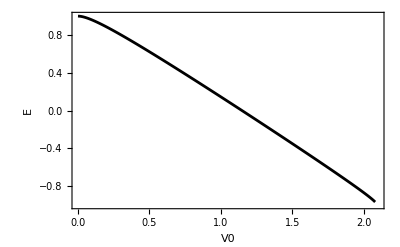

```mathematica
ListLinePlot[roots,FrameLabel->{"V0","E"},PlotRange->{{0,2.1},{-1,1}},Frame->True,PlotStyle->Black]
```

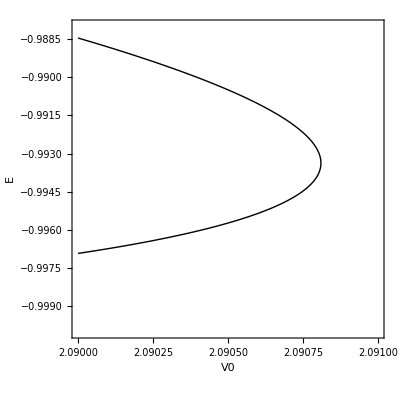

```mathematica
ContourPlot[eq16[En,V0],{V0,2.09,2.091},{En,-1,-0.988},Contours->{0},ContourStyle->{Thick,Black},ContourShading->None,FrameLabel->{"V0","E"},PlotPoints->60,MaxRecursion->4]
```

### Plot 2

We define equation 16 by parts for plotting :

```mathematica
Clear[L,a]
```

```mathematica
L=2;
a=2;
eq16[En_?NumericQ,V0_?NumericQ]:=Module[{s,g,l,y0,num1,den1,num2,den2,term1,term2},s=σ[En,a];
g=γ[En,V0,a];
l=λ[En,V0,a];
y0=(1+Exp[-a L])^-1;
(*first fraction*)num1=Hypergeometric2F1[3/2+g+s-l,3/2+g+s+l,2+2 s,y0];
den1=Hypergeometric2F1[1/2+g+s-l,1/2+g+s+l,1+2 s,y0];
term1=(1/2+g+s-l) (1/2+g+s+l) num1/den1;
(*second fraction*)num2=Hypergeometric2F1[3/2-g+s-l,3/2-g+s+l,2+2 s,y0];
den2=Hypergeometric2F1[1/2-g+s-l,1/2-g+s+l,1+2 s,y0];
term2=(1/2-g+s-l) (1/2-g+s+l) num2/den2;
(*whole left–hand side of (16)*)(term1+term2)/(1+2 s)+2 s (1+Exp[-a L])];
```

Finding the roots:

```mathematica
eq[En_,V0_]:=eq16[En,V0];

vList=Range[0.0,2.35,0.01];

roots=Reap[Module[{sol,Eguess=0.95},Do[sol=Quiet@FindRoot[eq[En,v]==0,{En,Eguess},WorkingPrecision->30,MaxIterations->80];
Eguess=En/. sol;(*use previous root as guess*)Sow[{v,Eguess}],{v,vList}]]][[2,1]];
```

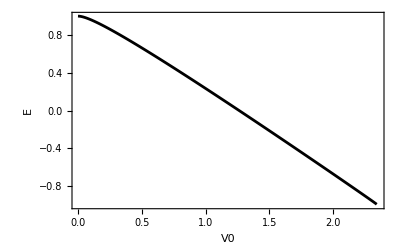

```mathematica
ListLinePlot[roots,FrameLabel->{"V0","E"},PlotRange->{{0,2.35},{-1,1}},Frame->True,PlotStyle->Black]
```

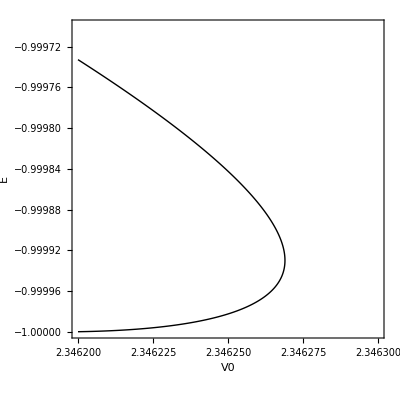

```mathematica
ContourPlot[eq16[En,V0],{V0,2.3462,2.3463},{En,-1,-0.99970},Contours->{0},ContourStyle->{Thick,Black},ContourShading->None,FrameLabel->{"V0","E"},PlotPoints->60,MaxRecursion->4]
```